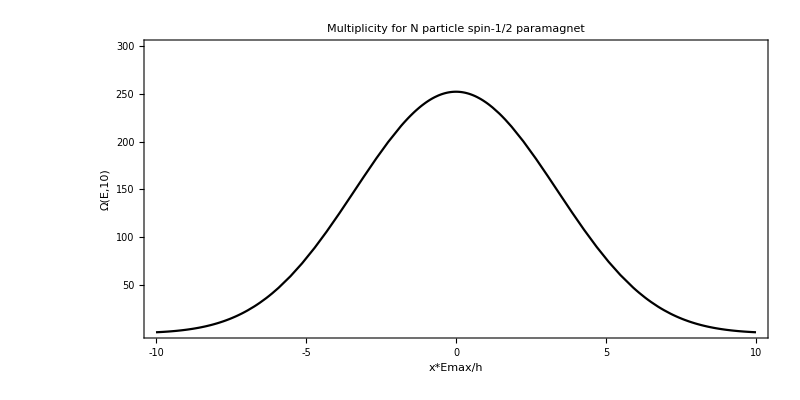

```mathematica
n=10;
Plot[n!/((n/2+ϵ/2)!(n/2-ϵ/2)!),{ϵ,-n,n},PlotLabel->Style["Multiplicity for N particle spin-1/2 paramagnet",Black,28],PlotRange->{{-n,n},{1,300}}(*,PlotLegends->Placed[{Style["",20], Style["E",20], Style["s2",20], Style["s3",20]},{0.8,0.8}]*), Frame->{{True,False},{True,False}},FrameLabel->{{Style["Ω(E,10)",Black,28],None},{Style["x*Emax/h",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Black},{Red, Dashed},{Blue, Dashed},{Green, Dashed}}]
Export["C:\\Users\\Sina\\Google Drive\\Spring 2021 Classes\\Statistical Mechanics\\HW1_p2b_image.png",%,ImageResolution->500];
```

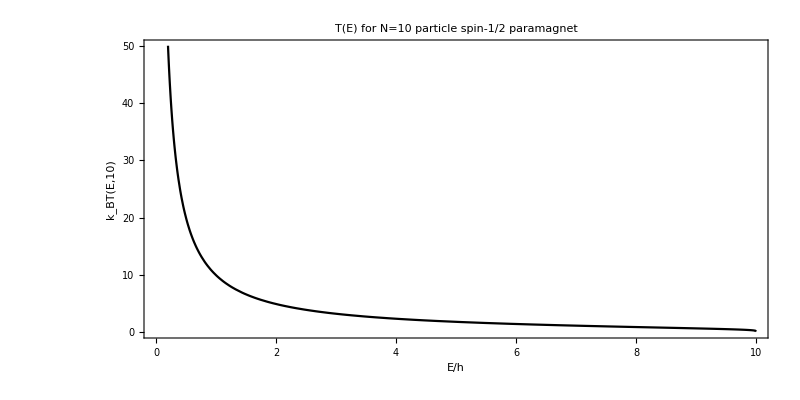

```mathematica
n=10;
Plot[2/Log[(n+ϵ)/(n-ϵ)],{ϵ,-n,n},PlotLabel->Style["T(E) for N=10 particle spin-1/2 paramagnet",Black,28],PlotRange->{{0,n},{0,50}}(*,PlotLegends->Placed[{Style["",20], Style["E",20], Style["s2",20], Style["s3",20]},{0.8,0.8}]*), Frame->{{True,False},{True,False}},FrameLabel->{{Style["k_BT(E,10)",Black,28],None},{Style["E/h",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Black},{Red, Dashed},{Blue, Dashed},{Green, Dashed}}]
Export["C:\\Users\\Sina\\Google Drive\\Spring 2021 Classes\\Statistical Mechanics\\HW1_p2c_image.png",%,ImageResolution->500];
```

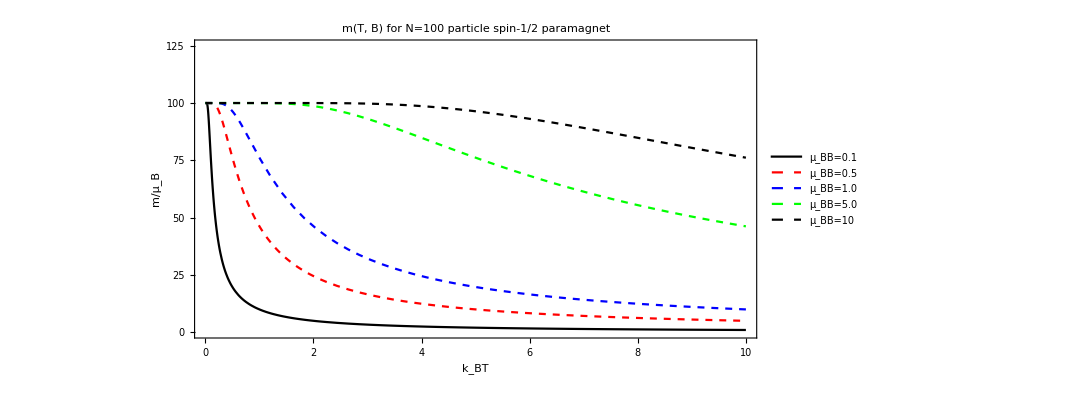

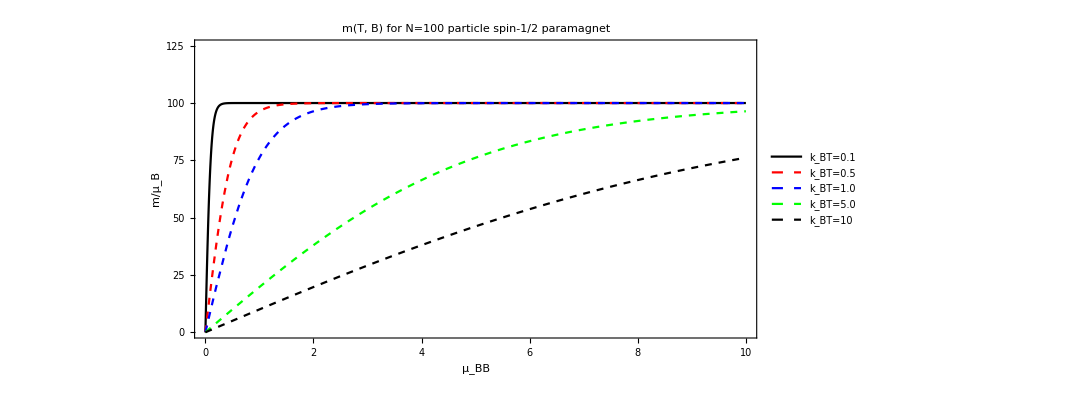

```mathematica
n=100;
Plot[Evaluate[n Tanh[B/t]/.B->{0.1,0.5,1,5,10}],{t,0,10},PlotLabel->Style["m(T, B) for N=100 particle spin-1/2 paramagnet",Black,28],PlotRange->{{0,10},{0,125}},PlotLegends->Placed[{Style["μ_BB=0.1",20], Style["μ_BB=0.5",20], Style["μ_BB=1.0",20], Style["μ_BB=5.0",20], Style["μ_BB=10",20]},{0.8,0.7}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["m/μ_B",Black,28],None},{Style["k_BT",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Black},{Red, Dashed},{Blue, Dashed},{Green, Dashed},{Black,Dashed}}]
Export["C:\\Users\\Sina\\Google Drive\\Spring 2021 Classes\\Statistical Mechanics\\HW1_p2d1_image.png",%,ImageResolution->500];Plot[Evaluate[n Tanh[B/t]/.t->{0.1,0.5,1,5,10}],{B,0,10},PlotLabel->Style["m(T, B) for N=100 particle spin-1/2 paramagnet",Black,28],PlotRange->{{0,10},{0,125}},PlotLegends->Placed[{Style["k_BT=0.1",20], Style["k_BT=0.5",20], Style["k_BT=1.0",20], Style["k_BT=5.0",20], Style["k_BT=10",20]},{0.8,0.3}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["m/μ_B",Black,28],None},{Style["μ_BB",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Black},{Red, Dashed},{Blue, Dashed},{Green, Dashed},{Black,Dashed}}]
Export["C:\\Users\\Sina\\Google Drive\\Spring 2021 Classes\\Statistical Mechanics\\HW1_p2d2_image.png",%,ImageResolution->500];
```

General::munfl: Exp[-4895.1] is too small to represent as a normalized machine number; precision may be lost.

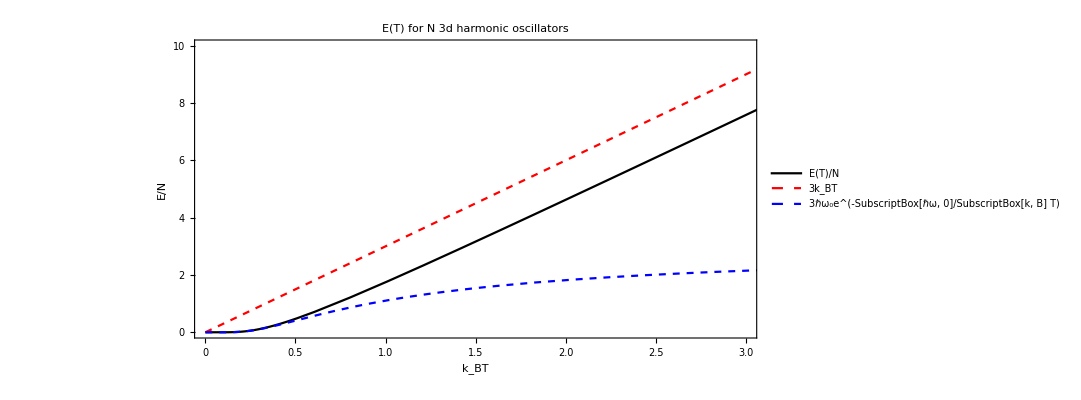

```mathematica
Plot[Evaluate[{3 (ℏ ω0)/(Exp[ℏ ω0/x]-1),3x,3ℏ ω0 Exp[-ℏ ω0/x]}/.{ℏ->1, ω0->1}],{x,0,10},PlotLabel->Style["E(T) for N 3d harmonic oscillators",Black,28],PlotRange->{{0,3},{0,10}},PlotLegends->Placed[{Style["E(T)/N",20], Style["3k_BT",20], Style["3ℏω_0e^(-SubscriptBox[ℏω, 0]/SubscriptBox[k, B] T)",20]},{0.2,0.75}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["E/N",Black,28],None},{Style["k_BT",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Black},{Red, Dashed},{Blue, Dashed},{Green, Dashed},{Black,Dashed}}]
Export["C:\\Users\\Sina\\Google Drive\\Spring 2021 Classes\\Statistical Mechanics\\HW1_p3c_image.png",%,ImageResolution->500];
```

General::munfl: 2.39621×10^7 1.4652490102×10^-4252 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4895.1] is too small to represent as a normalized machine number; precision may be lost.

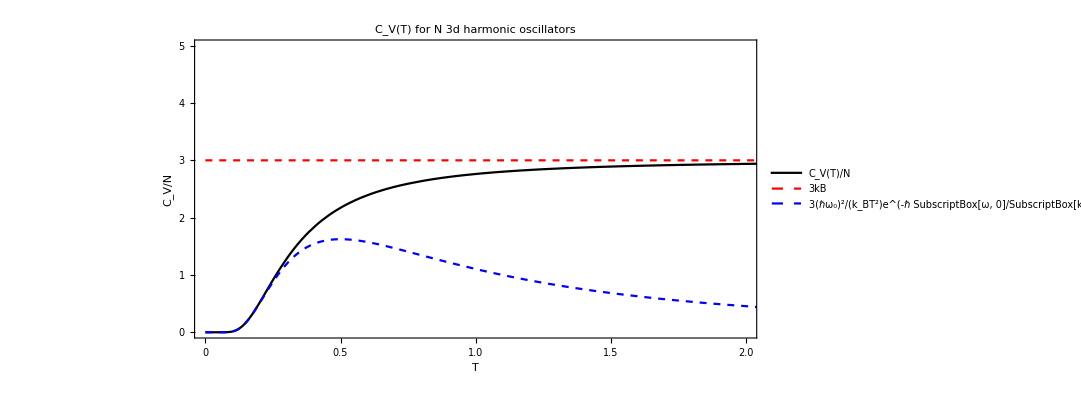

```mathematica
Plot[Evaluate[{3(ℏ ω0)^2/(kB T^2)*Exp[ℏ ω0/(kB T)]/(Exp[ℏ ω0/(kB T)]-1)^2,3 kB,3(ℏ ω0)^2/(kB T^2)Exp[-ℏ ω0/(kB T)]}/.{ℏ->1, ω0->1,kB->1}],{T,0,10},PlotLabel->Style["C_V(T) for N 3d harmonic oscillators",Black,28],PlotRange->{{0,2},{0,5}},PlotLegends->Placed[{Style["C_V(T)/N",20], Style["3kB",20], Style["3(ℏω_0)^2/(k_BT^2)e^(-ℏ SubscriptBox[ω, 0]/SubscriptBox[k, B] T)]",20]},{0.25,0.75}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["C_V/N",Black,28],None},{Style["T",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Black},{Red, Dashed},{Blue, Dashed},{Green, Dashed},{Black,Dashed}}]
Export["C:\\Users\\Sina\\Google Drive\\Spring 2021 Classes\\Statistical Mechanics\\HW1_p3d_image.png",%,ImageResolution->500];
```

```mathematica
S[T_,V_,n_]= 3 n kB/2(Log[kB T(1-2/(3n))]+Log[m/(2 Pi ℏ^2)])+n kB(Log[V]-Log[n])+kB Log[n/(kB T(3n/2-1))]+kB Log[3 Δ/2];
SE[En_,V_,n_]=3n kB/2 Log[2En/(3n)*(m/2 Pi ℏ^2)]+n kB Log[V/n]+kB Log[n/En*(3 Δ/2)]
```

kB n Log[V/n]+kB Log[(3 n Δ)/(2 En)]+3/2 kB n Log[(En m π ℏ^2)/(3 n)]

```mathematica
T[En_]=D[SE[En, V, n],En]
Solve[T[En]==1/T,En]
```

-kB/En+(3 kB n)/(2 En)

{{En→1/2 kB (-2+3 n) T}}

```mathematica
Ω[En_]=Δ/En (m/(2 Pi ℏ^2))^(3 n/2)(3 n V^n/2)En^(3n/2)/(n! (3n/2)!)
ΩT[T_]=FullSimplify[Ω[kB T(3n-2)/2]]
```

(3 2^(-1-(3 n)/2) En^(-1+(3 n)/2) n π^(-3 n/2) V^n Δ (m/ℏ^2)^(3 n/2))/(n! (3 n)/2!)

(3 8^-n n π^(-3 n/2) (kB (-2+3 n) T)^(-1+(3 n)/2) V^n Δ (m/ℏ^2)^(3 n/2))/(n! (3 n)/2!)

```mathematica
soln=Solve[ΩT[T]==1,T][[1]][[1]][[2]]
FullSimplify[soln*(3n-2)kB]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(3^(-2/(-2+3 n)) ((8^n π^(3 n/2) V^-n (m/ℏ^2)^(-3 n/2) n! (3 n)/2!)/(n Δ))^(2/(-2+3 n)))/(kB (-2+3 n))

9^(1/(2-3 n)) ((8^n π^(3 n/2) V^-n (m/ℏ^2)^(-3 n/2) Gamma[n] Gamma[1+(3 n)/2])/Δ)^(2/(-2+3 n))

```mathematica
Tc=N[2/(3n-2)(3 Δ n V^n/(n!(3n/2)!))^(2/(2-3n))(m/(2 Pi ℏ^2))^(-3n/(3n-2))/.{V->1,n->10,kB->1,m->1,ℏ->1, Δ->1}]
```

8.66113

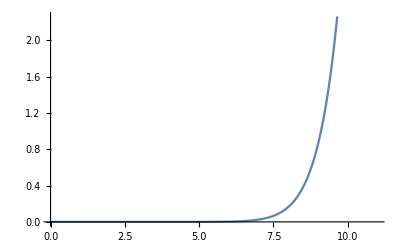

{T→9.10074}

```mathematica
Plot[ΩT[T]/.{V->1,n->10,kB->1,m->1,ℏ->1, Δ->1},{T,0,11}]
FindRoot[ΩT[T]-1/.{V->1,n->10,kB->1,m->1,ℏ->1, Δ->1},{T,8.66}]
```

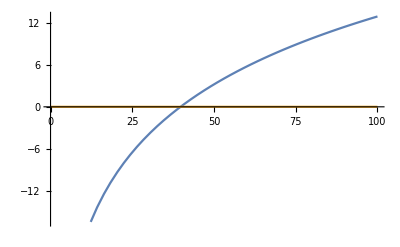

```mathematica
Plot[Evaluate[{S[T,V,n],2 Pi ℏ^2 n/(m n - 2m/3)(n/V)^(1-n/2)Δ^(3n/2-1)}/.{V->1,n->10,kB->1,m->1,ℏ->1, Δ->1}],{T,0,100}]
```

```mathematica
N[2 Pi ℏ^2 n/(m n - 2m/3)(n/V)^(1-n/2)Δ^(3n/2-1)/.{V->1,n->10,kB->1,m->1,ℏ->1, Δ->1}]
```

0.000673198

```mathematica
D[S[T,V,n],
```

$Aborted